```mathematica
outputDir =FileNameJoin[{ NotebookDirectory[],"/output"}];
importGenotypes[x_]:=Import[FileNameJoin[{outputDir,"genotypes_"<>ToString[x]<>".csv"}],"Table"];
importPhenotypes[x_]:=Import[FileNameJoin[{outputDir,"phenotypes_"<>ToString[x]<>".csv"}],"Table"];
importFitnesses[x_]:=Import[FileNameJoin[{outputDir,"fitnesses_"<>ToString[x]<>".csv"}],"List"];
arrayPlotGrid[list_]:=
Grid[ArrayPlot[#1]&/@list];
viewGeneration[x_]:=Grid[{ArrayPlot[CellularAutomaton[110,#,{100,All}]]&/@importGenotypes[x]}];
```

```mathematica
importGenotype[i_,j_]:=importGenotypes[i][[j]];
importPhenotypes[i_,j_]:=importPhenotypes[i][[j]];
importFitnesses[i_,j_]:=importFitnesses[i][[j]];
```

```mathematica
plotRow[x_]:=ArrayPlot[{x},Mesh->True]
```

```mathematica
mappingStats[gens_,phens_,i_]:=Map[{HammingDistance[gens⟦i⟧,gens⟦#⟧],HammingDistance[phens⟦i⟧,phens⟦#⟧]}&,Range[1,Length[gens]]];
fitnessStats[gens_,fits_,i_]:= Map[{HammingDistance[gens⟦i⟧,gens⟦#⟧],Abs[fits⟦i⟧-fits⟦#⟧]}&,Range[1,Length[gens]]];;
randomSamples[i_]:=Transpose[{RandomSample[Range[100],i],RandomSample[Range[100],i]}];
randomSample[i_,j_]:=Transpose[{ConstantArray[i,j],RandomSample[Range[100],j]}];
randomGenPhenMappings[sample_(*list of generation,genotype pairs*)]:=Flatten[mappingStats[importGenotypes[#1],importPhenotypes[#1],#2]&@@@sample,1];
randomGenFitMappings[sample_(*list of generation,genotype pairs*)]:=Flatten[fitnessStats[importGenotypes[#1],importFitnesses[#1],#2]&@@@sample,1];
pdf3D[points_]:=Plot3D[PDF[SmoothKernelDistribution[points],{x,y}],{x,0,100},{y,0,100},PlotRange->{0,MaxValue[PDF[SmoothKernelDistribution[points],{x,y}],{x,y}]}];
hist3D[points_]:=Histogram3D[points,Automatic,"PDF", ChartElementFunction->"GradientScaleCube",AxesLabel->{Framed["Hamming Distance, H",Background->White],Framed["Fitness, F",Background->White],Framed["P(F|H)",Background->White]},ViewPoint->{Front,Left,Top}];(*x: hamming distance, y: fitness, z: probability *)
```

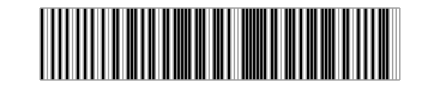
-Graphics3D--Graphics-

```mathematica
Labeled[hist3D[randomGenFitMappings[{{1,1}}]],plotRow[importGenotype[1,1]]]
```

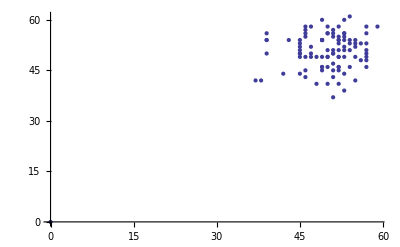

```mathematica
ListPlot[mappingStats[importGenotypes[1],importPhenotypes[1],1]]
```

```mathematica
d= SmoothKernelDistribution[mappingStats[importGenotypes[1],importPhenotypes[1],1]]
```

DataDistribution[«SmoothKernel»,{100,2}]

```mathematica
Plot3D[PDF[d,{x,y}],{x,0,100},{y,0,100}]
```

-Graphics3D-

```mathematica
Grid[Table[ListPlot[mappingStats[importGenotypes[i],importPhenotypes[i],j]],{i,1,20},{j,1,10}]]
```

```mathematica
Grid[Table[ListPlot[mappingStats[importGenotypes[i],importPhenotypes[i],j]],{i,1,20},{j,90,100}]]
```

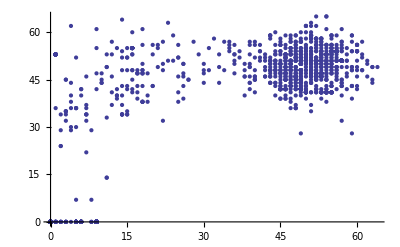

-Graphics3D-

```mathematica
sample=Transpose[{RandomSample[Range[50],20],RandomSample[Range[50],20]}];
points=Flatten[mappingStats[importGenotypes[#1],importPhenotypes[#1],#2]&@@@sample,1];
ListPlot[points]
d=SmoothKernelDistribution[points]
Plot3D[PDF[SmoothKernelDistribution[points],{x,y}],{x,0,100},{y,0,100}]
```

```mathematica
Plot3D[PDF[SmoothKernelDistribution[points],{x,y}],{x,0,100},{y,0,100},PlotRange->{0,MaxValue[PDF[SmoothKernelDistribution[points],{x,y}],{x,y}]}]
```

-Graphics3D-

```mathematica
Histogram3D[points]
```

-Graphics3D-

```mathematica
?Histogram3D
```

Histogram3D[{{x_1,y_1},{x_2,y_2},…}] plots a 3D histogram of the values {x_i,y_i}.
Histogram3D[{{x_1,y_1},{x_2,y_2},…},bspec] plots a 3D histogram with bins specified by bspec.
Histogram3D[{{x_1,y_1},{x_2,y_2},…},bspec,hspec] plots a 3D histogram with bin heights computed according to the specification hspec.
Histogram3D[{data_1,data_2,…}] plots 3D histograms for multiple datasets data_i.